```mathematica
Clear["Global`*"];
x=Range[100]/10;
y=x+1/2 x^2;
data=Transpose[{x,y}]
```

{{1/10,21/200},{1/5,11/50},{3/10,69/200},{2/5,12/25},{1/2,5/8},{3/5,39/50},{7/10,189/200},{4/5,28/25},{9/10,261/200},{1,3/2},{11/10,341/200},{6/5,48/25},{13/10,429/200},{7/5,119/50},{3/2,21/8},{8/5,72/25},{17/10,629/200},{9/5,171/50},{19/10,741/200},{2,4},{21/10,861/200},{11/5,231/50},{23/10,989/200},{12/5,132/25},{5/2,45/8},{13/5,299/50},{27/10,1269/200},{14/5,168/25},{29/10,1421/200},{3,15/2},{31/10,1581/200},{16/5,208/25},{33/10,1749/200},{17/5,459/50},{7/2,77/8},{18/5,252/25},{37/10,2109/200},{19/5,551/50},{39/10,2301/200},{4,12},{41/10,2501/200},{21/5,651/50},{43/10,2709/200},{22/5,352/25},{9/2,117/8},{23/5,759/50},{47/10,3149/200},{24/5,408/25},{49/10,3381/200},{5,35/2},{51/10,3621/200},{26/5,468/25},{53/10,3869/200},{27/5,999/50},{11/2,165/8},{28/5,532/25},{57/10,4389/200},{29/5,1131/50},{59/10,4661/200},{6,24},{61/10,4941/200},{31/5,1271/50},{63/10,5229/200},{32/5,672/25},{13/2,221/8},{33/5,1419/50},{67/10,5829/200},{34/5,748/25},{69/10,6141/200},{7,63/2},{71/10,6461/200},{36/5,828/25},{73/10,6789/200},{37/5,1739/50},{15/2,285/8},{38/5,912/25},{77/10,7469/200},{39/5,1911/50},{79/10,7821/200},{8,40},{81/10,8181/200},{41/5,2091/50},{83/10,8549/200},{42/5,1092/25},{17/2,357/8},{43/5,2279/50},{87/10,9309/200},{44/5,1188/25},{89/10,9701/200},{9,99/2},{91/10,10101/200},{46/5,1288/25},{93/10,10509/200},{47/5,2679/50},{19/2,437/8},{48/5,1392/25},{97/10,11349/200},{49/5,2891/50},{99/10,11781/200},{10,60}}

```mathematica
result=NonlinearModelFit[data,a0+a1 t+a2 t^2,{a0,a1,a2},t]
```

FittedModel[-4.96249×10^-15+1. t+0.5 t^2]

```mathematica
result["ParameterTable"]
```

```mathematica
f=result["Function"]
```

-4.96249×10^-15+1. #1+0.5 #1^2&

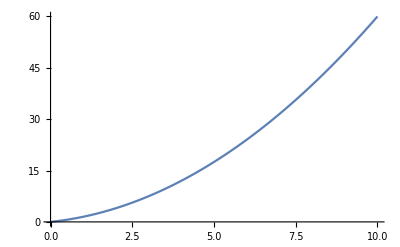

```mathematica
Plot[f[xx],{xx,0,10}]
```

```mathematica
result["ParameterTable"]
```

General::munfl: Exp[-3024.54] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

General::munfl: Exp[-3184.69] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

| Estimate | Standard Error | t-Statistic | P-Value
a0 | -4.96249×10^-15 | 6.55081×10^-15 | -0.757539 | 0.450564
a1 | 1. | 2.9939×10^-15 | 3.34013×10^14 | 0.
a2 | 0.5 | 2.87193×10^-16 | 1.74099×10^15 | 0.